```mathematica
C[t]=C*E^(Sin[w*t+p])*(P1/Log[D1+1]+P2/Log[D2+1]+P3/Log[D3+1])
```

Set::write: Tag C in C[t] is Protected.

```mathematica
C ⅇ^Sin[p+t w] (P1[t]/Log[1+D1]+P2[t]/Log[1+D2]+P3[t]/Log[1+D3]+1)
```

C ⅇ^Sin[p+t w] (1+5.38409 {8,4,8,16,12,7,9,15}[t]+5.13278 {8,10,15,31,6,1,3,9}[t]+4.79111 {12,2,5,5,11,7,9,17}[t])

```mathematica
C ⅇ^Sin[p+t w] ((C1*P1[t])/Log[1+D1]+(C2*P2[t])/Log[1+D2]+(C3*P3[t])/Log[1+D3])
```

C ⅇ^Sin[p+t w] ((C1 P1[t])/Log[1+D1]+(C2 P2[t])/Log[1+D2]+(C3 P3[t])/Log[1+D3])

```mathematica
{p,w,C,C1,C2,C3}
```

{p,w,C,C1,C2,C3}

```mathematica
D1=0.1302
D2=0.2378
D3=0.3146
```

0.1302

0.2378

0.3146

```mathematica
dt={197,147,132,172,146,174,160,203}
```

{197,147,132,172,146,174,160,203}

```mathematica
P1={32,0,0,41,2,0,2,2}
P2={17,17,4,13,16,2,21,14}
P3={222,229,180,195,133,110,117,111}
```

{32,0,0,41,2,0,2,2}

{17,17,4,13,16,2,21,14}

{222,229,180,195,133,110,117,111}

```mathematica
{222,229,180,195,133,110,117,111}
```

```mathematica
{222,229,180,195,133,110,117,111}
```

```mathematica
{222,229,180,195,133,110,117,111}
```

```mathematica
FindFit[dt,C ⅇ^Sin[p+t w] ((C1 P1[[t]])/E^(1+D1)+(C2 P2[[t]])/E^(1+D2)+(C3  P3[[t]])/E^(1+D3)),{p,w,C,C1,C2,C3},t]
Show[ListPlot[dt,PlotStyle->Red],Plot[C ⅇ^Sin[p+t w] ((C1 P1[[t]])/Log[1+D1]+(C2 P2[[t]])/Log[1+D2]+(C3  P3[[t]])/Log[1+D3])/.{p->4.128912570584698,w->0.2831323593734609,C->1.9329574432254837,C1->1.9473478273474547,C2->-6.519356689215801,C3->4.2486539612496514},{t,1,8}]]
```

Part::pkspec1: The expression t cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{p→4.12891,w→0.283132,C→1.93296,C1→1.94735,C2→-6.51936,C3→4.24865}

Part::pkspec1: The expression 1.00014 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

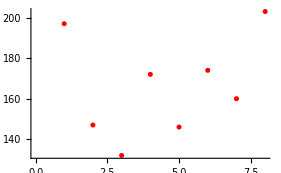
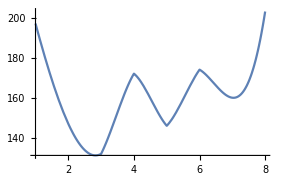

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pkspec1: The expression 1.00014 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pkspec1: The expression t cannot be used as a part specification.

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{p→4.12891,w→0.283132,C→0.815014,C1→0.182568,C2→-0.956656,C3→0.740277}

```mathematica
Graphics[Point[Table[{t,C ⅇ^Sin[p+t w] ((C1 P1[[t]])/E^[1+D1]+(C2 P2[[t]])/E^[1+D2]+(C3  P3[[t]])/E^[1+D3])/.{p->-0.33383777172676926,w->1.6295200413268334,C->0.17761376541577517,C1->-3.4639675758326534,C2->2.550932287531774,C3->1.8115220583878224}},{t,1,8}]],AspectRatio->1/GoldenRatio,Axes->True,PlotRange->All]
```

Part::pkspec1: The expression 1.00014 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

```mathematica
{197,147,132,172,146,174,160,203}
```

```mathematica
Plot[{197,147,132,172,146,174,160,203}]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[{197,147,132,172,146,174,160,203}]

```mathematica
Interpolation[{197,147,132,172,146,174,160,203}]
```

InterpolatingFunction[{{1, 8}}, <>]

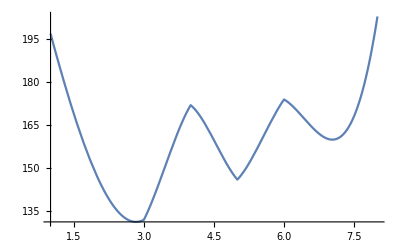

```mathematica
Plot[InterpolatingFunction[{{1,8}},{5,3,0,{8},{4},0,0,0,0,Automatic,{},{},False},{{1,2,3,4,5,6,7,8}},{{197},{147},{132},{172},{146},{174},{160},{203}},{Automatic}][x],{x,1,8}]
```